# Project

Wang Long	1101110160		
Work in Mathematica 8.0.0. Main codes are hidden. Please read project.nb in Mathematica to get all codes.

## Data set

### Data Import (...)

```mathematica
data=Import["/Users/wanglong/Dropbox/Datas/diffuse/spSpec-53786-1850-209.fit",{"RawData"}][[1]];
head=Import["/Users/wanglong/Dropbox/Datas/diffuse/spSpec-53786-1850-209.fit",{"Metadata"}][[1]];
```

```mathematica
linedata={{"[Ne V]",3345,"2p^2^3P_1 ← 2p^2^1D_2"，2.09,1,3},{"[Ne V]",3425,"2p^2^3P_2 ← 2p^2^1D_2",2.09,1,5},{"[O II]",3727,"2p^3^4S_(3/2) ← 2p^3^2D_(3/2, 5/2)",1.34,1,4},{"[Ne III]",3868,"2p^4^3P_2 ← 2p^4^1D_2",1.36,1,5},{"Hζ",3889,"2 ← 8",0,2,1},{"[Ne III]",3967,"2p^4^3P_1 ← 2p^4^1D_2",1.36,1,3},{"Hδ",4102,"2 ← 6",3.02*^-14*0.259,0,1},{"Hγ",4341,"2 ← 5",3.02*^-14*0.468,0,1},{"[O III]",4363,"2p^2^1D_2 ← 2p^2^1S_0",0.58,1,5},{"He I",4471,"2p^3P_(0, 1, 2) ← 4d^3D_(1, 2, 3)",1.39*^-14,0,1},{"He II",4686,"3 ,← 4",3.57*^-13,0,1},{"Hβ",4861,"2 ← 4",3.02*^-14,0,1},{"[O III]",4959,"2p^2^3P_1 ← 2p^2^1D_2",2.29,1,3},{"[O III]",5007,"2p^2^3P_2 ← 2p^2^1D_2",2.29,1,5},{"[N I]",5200,"2p^3^4S_(3/2) ← 2p^3^2D_(3/2, 5/2)",0.62,1,4},(*p406*){"[N II]",5755,"2p^2^1D_2 ← 2p^2^1S_0",0.83,1,5},(*p53,56*){"He I",5876,"2p^3P_(0, 1, 2) ← 3d^3D_(1, 2, 3)",1.39*^-14*2.67,0,1},{"[O I]",6300,"2p^4^3P_2 ← 2p^4^1D_2",0.38,1,5},{"[O I]",6364,"2p^4^3P_1 ← 2p^4^1D_2",0.38,1,3},{"[N II]",6548,"2p^2^3P_1 ← 2p^2^1D_2",2.64,1,3},{"Hα",6563,"2 ← 3",3.02*^-14*2.863,0,1},{"[N II]", 6584,"2p^2^3P_2 ← 2p^2^1D_2",2.64,1,5},{"He I",6678,"2p^1P_1 ← 3d^1D_2",1.39*^-14*0.756,0,1},{"[S II]",6716,"3p^3^4S_(3/2) ← 3p^3^2D_(5/2)",6.9*3/5,1,4},{"[S II]",6731,"3p^3^4S_(3/2) ← 3p^3^2D_(3/2)",6.9*2/5,1,4},{"He I",7065,"2p^3P_(0, 1, 2) ← 3d^3S_1",1.39*^-14*0.489,0,1},{"[Ar III]",7135,"3p^4^3P_2 ← 3p^4^1D_2",4.83,1,5},{"[O II]",7320,"2p^3^2D_(5/2) ← 2p^3^2P_(1/2, 3/2)",0.33,1,6},{"[O II]",7331,"2p^3^2D_(3/2) ← 2p^3^2P_(1/2, 3/2)",1.0,1,4}};
```

```mathematica
siipoint={{72.0068,385.002},{88.2866,385.002},{107.071,385.002},{128.36,385.002},{150.901,383.75},{169.686,382.498},{192.227,381.246},{214.768,378.741},{237.309,376.236},{258.598,369.975},{279.887,363.713},{298.672,354.947},{314.951,344.929},{332.483,331.154},{346.259,318.631},{357.529,307.36},{366.295,296.09},{376.314,286.071},{386.332,274.801},{395.098,264.782},{407.621,252.259},{416.387,240.989},{427.658,229.718},{437.676,218.448},{448.947,208.429},{458.965,199.663},{472.74,190.897},{485.263,182.131},{497.786,175.87},{510.309,168.356},{525.336,164.599},{539.112,160.842},{552.887,158.338},{565.41,155.833},{581.69,153.328},{595.465,150.824},{614.249,150.824},{629.277,150.824},{640.547,150.824}};
siixaxis={{73.2591,49.3882},{643.052,50.6404}};
siiyaxis={{73.2591,49.3882},{72.0068,425.076}};
rnfigdata={(#1-siixaxis[[1,1]])*5/(siixaxis[[2,1]]-siixaxis[[1,1]]),(#2-siiyaxis[[1,2]])*1.6/(siiyaxis[[2,2]]-siiyaxis[[1,2]])}&@@@siipoint;
```

### Header

```mathematica
MenuView[head]
```

## Data Reducing

### Globular Function (...)

```mathematica
(*Plot spectrum*)
Plotspec[plotdata_,plotlabel_,size_]:=ListPlot[plotdata,Joined->True,PlotRange->Full,AxesLabel->{"λ[Å]","F_λ[10^-17erg cm^-2s^-1Å^-1]"},PlotLabel->plotlabel,AxesOrigin->Min/@Transpose@plotdata,ImageSize->size]
Plotfit[specdata_,peakpoint_,fitspec_,size_]:=Show[{Plotspec[specdata,"Redshifted corrected spectrum",size],ListPlot[peakpoint,PlotStyle->Green,PlotMarkers->"X"]}~Join~Table[Plot[fitspec[[i]][x],{x,peakpoint[[i,1,1]]-100,peakpoint[[i,-1,1]]+100},PlotStyle->Red,PlotRange->Full],{i,Length@fitspec}],ImageSize->size]
Plotfitcheck[specdata_,peakpoint_,fitspec_,index_]:=Manipulate[ListPlot[specdata,Joined->False,PlotRange->{{peakpoint[[i,1,1]]-ki,peakpoint[[i,-1,1]]+ki},{-10,Max@peakpoint[[i,All,2]]}},AxesLabel->{"λ[Å]","F_λ[10^-17erg cm^-2s^-1Å^-1]"},PlotLabel->"Fit check",Epilog->First@Plot[fitspec[[i]][x],{x,peakpoint[[i,1,1]]-ki,peakpoint[[i,-1,1]]+ki},PlotStyle->Red,PlotRange->Full]],{{i,index,"No."},1,Length@fitspec,1},{{ki,100,"x-axis range"},1,100,1},Paneled->False]
(*Fit spectrum*)
Polynomial[x_,n_]:=Plus@@Table[x^i*a[i],{i,0,n}]
Gauss[x_,n_]:=Plus@@Table[A[i]*Exp[-(x-μ[i])^2/(2σ[i])^2],{i,n}]
Fitspec[fitdata_,λinter_,fluxrange_,background_,peakpoint_,range_]:=NonlinearModelFit[Select[fitdata,peakpoint[[1,1]]-range<#[[1]]<peakpoint[[Length@peakpoint,1]]+range/2&],{a0+Gauss[x,Length@peakpoint],background[[1]]<a0<background[[2]]}~Join~Flatten@Table[{peakpoint[[i,2]]-fluxrange<A[i]<peakpoint[[i,2]]+fluxrange,peakpoint[[i,1]]-λinter/2<μ[i]<peakpoint[[i,1]]+λinter/2,0<σ[i]<λinter},{i,Length@peakpoint}],{{a0,0}}~Join~Flatten[Table[{{A[i],peakpoint[[i,2]]},{μ[i],peakpoint[[i,1]]},{σ[i],5λinter}},{i,Length@peakpoint}],1],x]
Fitspecs[fitdata_,peakpoint_,fluxrange_,range_,λinter_,background_]:=Table[Fitspec[fitdata,λinter,fluxrange,background,peakpoint[[j]],range],{j,Length@peakpoint}]
Fitpars[fitspec_]:=#1~Join~#2&@@@Transpose@({Table[{i},{i,Length@#}],#}&@Flatten[Table[Flatten@Prepend[#,{fitspec[[i]]["ParameterTableEntries"][[1,1]]}]&/@Partition[fitspec[[i]]["ParameterTableEntries"][[2;;,1]],3],{i,Length@fitspec}],1])
(*Fit peaks*)
Fitpeak[fitdata_,onepeakpoint_,λinter_,minflux_,background_]:=NonlinearModelFit[fitdata,{a0+A*Exp[-(x-μ)^2/(2 σ^2)],onepeakpoint[[2]]-50<A<onepeakpoint[[2]]+50,background[[1]]<a0<background[[2]],onepeakpoint[[1]]-λinter/2<μ<onepeakpoint[[1]]+λinter/2,0<σ<10*λinter},{{a0,0},{A,onepeakpoint[[2]]},{μ,onepeakpoint[[1]]},{σ,5λinter}},x]
Fitpeaks[fitdata_,pointpeakdata_,minflux_,range_,λinter_,background_]:=Table[Fitpeak[Select[fitdata,pointpeakdata[[i,1]]-2*range<#[[1]]<pointpeakdata[[i,1]]+2*range&],peakpoint[[i]],λinter,minflux,background(*-peakpoint[[i,1]]/400*)],{i,Length@peakpoint}]
(*Find peaks*)
Findpeak[specdata_,minflux_,λinter_]:=Split[Sort[Select[specdata,#[[2]]>minflux&]],#2[[1]]-#1[[1]]<λinter&]
Findpeakvalue[findpeakdata_]:=Table[Max@findpeakdata[[i,All,2]]/.(#[[2]]->#&/@findpeakdata[[i]]),{i,Length@findpeakdata}]
cond1[peakdata_,minflux_,λinter_]:=Flatten@Table[{A[i]>minflux,0<σ[i]<λinter,peakdata[[i,1]]-λinter/2<μ[i]<peakdata[[i,1]]+λinter/2},{i,Length@peakpoint}]
(*Line Match*)
αeff[q_,mac_,w1_,T_,λ_]:=Piecewise[{{8.629*^-6*q/(w1*T^(1/2))*Exp[-6.62606896*^-34*3*^18/λ/(1.3806504*^-23*T)],mac==1},{q,mac==0},{"--",mac==2}}]
Matchline[fitspec_,linedat_,err_,T_]:=Cases[Select[Table[linedat[[i]]~Join~Flatten@({Length@#,#}&@Select[fitspec,Abs@(#[[4]]-linedat[[i,2]])<err&]),{i,Length@linedat}],#[[7]]≥1&],{name_,λ_,p_,q_,mac_,w1_,match_,no_,a0_,A_,λo_,σ_}->{name,λ,p,λo,A*√(2π)σ,a0,A,σ,αeff[q,mac,w1,T,λo]}]
Lineref[matchlinedata_,index_]:=#[[index]]->#&/@matchlinedata
```

### Origin spectrum (Linear scale)

Use the second column of spSpec-53786-1850-209.fit. Figure 1 is the original spectrum subtracting continuum spectrum.

#### Code (...)

```mathematica
step=({"COEFF0","COEFF1"}/.head)[[All,1]];
spec1=Table[{10^(step[[1]]+i*step[[2]]),data[[2,i]]},{i,Length@data[[1]]}];
```

#### Plot

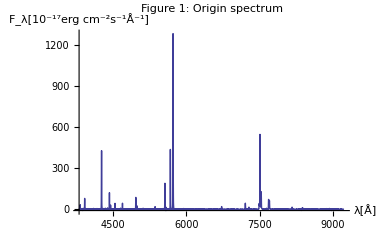

```mathematica
Plotspec[spec1,"Figure 1: Origin spectrum",380]
```

### Galactic extinction correction

Galactic extinction corrected flux F_0(λ)=F_obs(λ)×10^c[1+f(λ)], where f(λ) is standard extinction curve, c = 0.4 (R+0.53) E(B-v). f(λ) is calculated by using dmdered code (Figure 2). The imput parameters are listed in Table 1. Method ‘0’ means:  λ < 3640 Å, Seaton Gal; λ > 3640 Å, Howarth Gal.
	Figure 3 shows Galactic extinction corrected spectrum.

#### Code (...)

```mathematica
R=3.1;
c=0.4(R+0.53)*("SFD_EBV"/.head)[[1]];
```

```mathematica
fλdata=Import["/Users/wanglong/data/diffuse/dmdered.dat","Data"];
dmdered=Import["/Users/wanglong/data/diffuse/dmdered.cof","Table"];
fλ=Interpolation[fλdata];
spec2={#1,#2*10^(c*(1+fλ[#1]))}&@@@spec1;
```

```mathematica
Plotfλ:=Plot[fλ[x],{x,dmdered[[1,1]],dmdered[[1,2]]},PlotRange->Full,AxesOrigin->{dmdered[[1,1]],fλ[dmdered[[1,2]]]},AxesLabel->{"λ[Å]","fλ"},PlotLabel->"Figure 2: standard extinction curve",ImageSize->400]
Dmderedcof:="Table 1: dmdered input parameters: \n"Grid[{{"λMin","λMax","step","R","Method","c","E(B-V)"},Flatten@{dmdered,("SFD_EBV"/.head)[[1]]}},Frame->All]
```

#### Plot

Table 1: dmdered input parameters: 
 λMin | λMax | step | R | Method | c | E(B-V)
3200 | 9300 | 1 | 3.1 | 0 | 0.0657233 | 0.045264

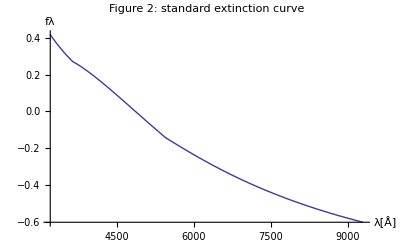

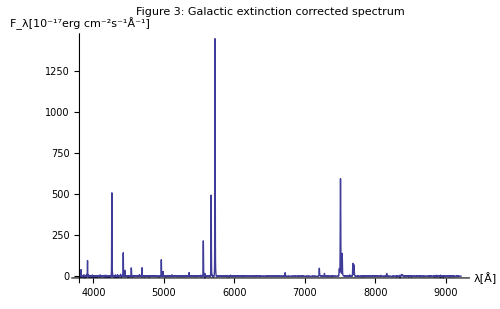

```mathematica
Dmderedcof
Plotfλ
Plotspec[spec2,"Figure 3: Galactic extinction corrected spectrum",500]
```

### Redshift correction

Redshift corrected flux: F_1=(F_0(1+z))^3, corrected wavelength: λ_1=λ_obs/(1+z). Figure 4 is redshift corrected one.

#### Code (...)

```mathematica
redshift=("Z"/.head)[[1]];
spec3={#1/(1+redshift),#2*(1+redshift)^3}&@@@spec2;
```

#### Plot

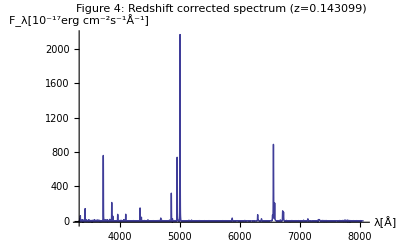

```mathematica
Plotspec[spec3,"Figure 4: Redshift corrected spectrum (z="<>ToString@redshift<>")",400]
```

### Local extinction correction

To do correction for the local extinction. First we should calculate c(Hβ) by using equation: 
			(I(H_*))/(I(Hβ))=((I(H_*))_t)/((I(Hβ))_t)×10^(-c_i[f(H_*)-f(Hβ)])
	where * are Hα, Hγ and Hδ, t refer to theoretical ratios Then c(Hβ)=∑c_i.
	The local extinction corrected flux F_2=F_1×10^(c(Hβ) [1+f(λ)])
	To calculat I, we should first fit Hydrogen lines by gaussian function c0+A Exp[-(x-μ)^2/(2σ)^2]. Then I=∫[F_1(λ)-F_c(λ)]ⅆλ=√(2π)σ A, where ‘c’ is cotinuum spectrum flux.
	Table 3 shows the calculated I and c_i. Figure 5 shows local extinction corrected spectrum.

#### Code (...)

```mathematica
Off[NonlinearModelFit::eit]
fitpeak=Findpeak[spec3,50,5];
peakpoint=Split[Findpeakvalue[fitpeak],#2[[1]]-#1[[1]]<40&];
```

```mathematica
Off[FittedModel::constr]
fitspec1=Fitspecs[spec3,peakpoint,25,16,3,{0,10}];
```

```mathematica
Off[Solve::ifun]
fitspecpar1=Fitpars[fitspec1];
linematchdata1=Matchline[fitspecpar1,linedata,3,10^4];
linerefdata1=Lineref[linematchdata1,1];
Iαβ=2.85;Iγβ=0.469;Iδβ=0.26;
I0={Iαβ,Iγβ,Iδβ};
cc[a_,b_,i_]:=c1/.Solve[(a/.linerefdata1)[[5]]/(b/.linerefdata1)[[5]]==i*10^(-c1*(fλ[(a/.linerefdata1)[[2]]]-fλ[(b/.linerefdata1)[[2]]])),c1][[1,1]]
ctable={cc["Hα","Hβ",Iαβ],cc["Hγ","Hβ",Iγβ],cc["Hδ","Hβ",Iδβ]};
ca=Plus@@ctable/3;
spec4={#1,#2*10^(ca*(1+fλ[#1]))}&@@@spec3;
```

```mathematica
Ctable:="Table 2: parameters and calculated c: (c_i in last Row is c(Hβ))\n"Grid[{{"Line","λ[Å]","I_line","I*_0/I(Hβ)_0","c_i"}}~Join~Table[Flatten@Append[#[[i]],{I0[[i]],ctable[[i]]}],{i,Length@ctable}]&@((#/.linerefdata1)[[{1,4,5}]]&/@{"Hα","Hγ","Hδ"})~Join~{(("Hβ"/.linerefdata1)[[{1,4,5}]])~Join~{"",ca}},Frame->All]
```

#### Plot

```mathematica
Ctable
```

Table 2: parameters and calculated c: (c_i in last Row is c(Hβ))
 Line | λ[Å] | I_line | I*_0/I(Hβ)_0 | c_i
Hα | 6565.45 | 4665.98 | 2.85 | 0.389793
Hγ | 4342.19 | 520.337 | 0.469 | 0.348973
Hδ | 4103.25 | 250.275 | 0.26 | 0.583093
Hβ | 4863.28 | 1228.21 |  | 0.44062

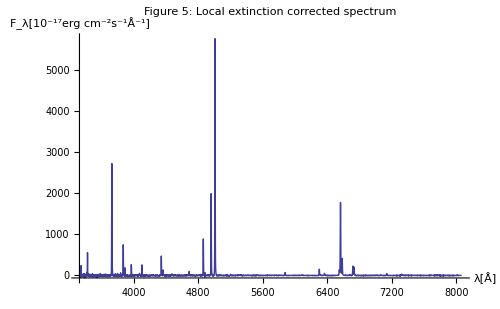

```mathematica
Plotfitcheck[spec3,peakpoint,fitspec1,8]
Plotspec[spec4,"Figure 5: Local extinction corrected spectrum",500]
```

### Flux normalization

Again we use gaussian function to fit all lines with peak fluxs larger than 50×10^-17 erg cm^-2 s^-1 Å^-1. Then we get flux normalization by F_3(λ)=F_2(λ)×100/I(Hβ).

#### Code (...)

```mathematica
Off[NonlinearModelFit::eit]
fitpeak21=Findpeak[spec4,100,3];
peakpoint21=Findpeakvalue[fitpeak21];
fitpeak22=Findpeak[spec4,40,3];
peakpoint22=Findpeakvalue[fitpeak22];
peakpoint2=Split[peakpoint22∪peakpoint21,#2[[1]]-#1[[1]]<40&];
```

```mathematica
Off[FittedModel::constr]
fitspec2=Fitspecs[spec4,peakpoint2,50,16,3,{0,10}];
```

```mathematica
Off[Solve::ifun]
fitspecpar2=Fitpars[fitspec2];
linematchdata2=Matchline[fitspecpar2,linedata,3.5,14321];
linerefdata2=Lineref[linematchdata2,1];
spec5={#1,100*#2/("Hβ"/.linerefdata2)[[5]]}&@@@spec4;
```

```mathematica
Plotnormspec:=ListPlot[spec5,Joined->True,AxesLabel->{"λ[Å]","Normalized Flux"},PlotLabel->"Figure 6: Flux normalized spectrum",AxesOrigin->Min/@Transpose@spec5,PlotRange->Full,ImageSize->450]
```

#### Plot

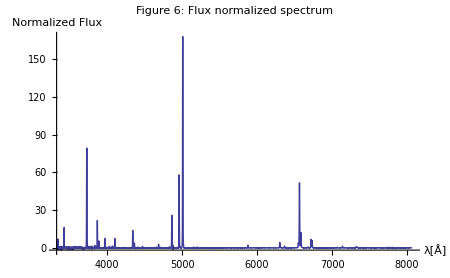

```mathematica
Plotfitcheck[spec4,peakpoint2,fitspec2,16]
Plotnormspec
```

### Emission line measurements

Used flux normalized spectrum, we can also calculate the normalized line strength I(norm). The result are listed int Table 3.

#### Code (...)

```mathematica
linematchdata3=Cases[linematchdata2,{n_,l_,p_,lo_,i_,a0_,A_,s_,α_}->{n,l,p,lo,100*i/("Hβ"/.linerefdata2)[[5]],α,a0,A,s}];
```

```mathematica
Linetable:="Table 3: Gaussian emission lines fit paramenters \n"Grid[{{"Line","λ[Å]","Transition","λ_obs[Å]","I_line(norm)","α_eff"}}~Join~linematchdata3[[All,1;;6]],Frame->All]
```

#### Plot

```mathematica
Linetable
```

Table 3: Gaussian emission lines fit paramenters 
 Line | λ[Å] | Transition | λ_obs[Å] | I_line(norm) | α_eff
[Ne V] | 3425 | 2p^2^3P_2 ← 2p^2^1D_2 | 3426.56 | 40.3644 | 1.60296×10^-9
[O II] | 3727 | 2p^3^4S_(3/2) ← 2p^3^2D_(3/2, 5/2) | 3728.94 | 339.039 | 1.62975×10^-9
[Ne III] | 3868 | 2p^4^3P_2 ← 2p^4^1D_2 | 3870.04 | 64.8931 | 1.45994×10^-9
Hζ | 3889 | 2 ← 8 | 3890.44 | 15.7994 | --
[Ne III] | 3967 | 2p^4^3P_1 ← 2p^4^1D_2 | 3969.97 | 32.1801 | 2.59767×10^-9
Hδ | 4102 | 2 ← 6 | 4103.25 | 24.2556 | 7.8218×10^-15
Hγ | 4341 | 2 ← 5 | 4342.19 | 47.3624 | 1.41336×10^-14
[O III] | 4363 | 2p^2^1D_2 ← 2p^2^1S_0 | 4364.47 | 11.1128 | 8.35666×10^-10
He II | 4686 | 3 ,← 4 | 4687.04 | 10.119 | 3.57×10^-13
Hβ | 4861 | 2 ← 4 | 4863.28 | 100. | 3.02×10^-14
[O III] | 4959 | 2p^2^3P_1 ← 2p^2^1D_2 | 4960.62 | 218.313 | 7.25295×10^-9
[O III] | 5007 | 2p^2^3P_2 ← 2p^2^1D_2 | 5008.56 | 653.798 | 4.437×10^-9
He I | 5876 | 2p^3P_(0, 1, 2) ← 3d^3D_(1, 2, 3) | 5878.1 | 10.1498 | 3.7113×10^-14
[O I] | 6300 | 2p^4^3P_2 ← 2p^4^1D_2 | 6302.63 | 19.0887 | 1.1118×10^-9
[O I] | 6364 | 2p^4^3P_1 ← 2p^4^1D_2 | 6366.09 | 5.35507 | 1.8827×10^-9
[N II] | 6548 | 2p^2^3P_1 ← 2p^2^1D_2 | 6551.14 | 23.2414 | 1.36765×10^-8
Hα | 6563 | 2 ← 3 | 6565.45 | 274.739 | 8.64626×10^-14
[N II] | 6584 | 2p^2^3P_2 ← 2p^2^1D_2 | 6585.92 | 63.9118 | 8.2727×10^-9
[S II] | 6716 | 3p^3^4S_(3/2) ← 3p^3^2D_(5/2) | 6719.07 | 31.9166 | 1.67144×10^-8
[S II] | 6731 | 3p^3^4S_(3/2) ← 3p^3^2D_(3/2) | 6733.41 | 29.8454 | 1.11785×10^-8

### Plasma diagnostics

From Table 3, we can then estimate the electron density n_e and temperature T_e. Since the resolution of this spectrum cannot use [O II] (3729,3726) lines to calculate n_e. We can use [S II] (6716,6731) to calculate n_e. From Figure 7 we can see that if we get I(λ6716) / I(λ6731), we can get a related electron density n_e. The result is listed in Table 4. 
	To calculate T_e, we can use [O III] lines (4959, 5007 and 4363). The equation to calculate T_e for [O III] is:
		(I (λ4959) + I (λ5007))/(I (λ4363))=(7.90 exp(3.29×10^4/T_e))/(1+4.5×10^-4 N_e/T_e^(1/2))
	For [N II] and [Ne III], we cannot get I(λ5755) and I(λ3343) from the spectrum, so we cannot use them to calculate T_e.

#### Code (...)

```mathematica
fig1=Import["/Users/wanglong/Dropbox/Datas/diffuse/fig1.tiff","Tiff"];
linerefdata3=Lineref[linematchdata3,2];
rnfig=Interpolation[rnfigdata[[4;;-4,{2,1}]]];
Iab[a_,b_]:=(a/.linerefdata3)[[5]]/(b/.linerefdata3)[[5]]
```

```mathematica
(*[S II]*)
sii={"[S II] (I (λ6716))/(I (λ6731))",Iab[6716,6731],10^rnfig[Iab[6716,6731]]};
```

```mathematica
(*[O III]*)
Off[Solve::ratnz]
Iλ[λ_]:=(λ/.linerefdata3)[[5]]
oiii={"[O III] (I (λ4959) + I (λ5007))/(I (λ4363))"}~Join~({#,t/.NSolve[#==7.90Exp[3.29*^4/t]/(1+4.5*^-4 sii[[3]]/t^(1/2)),t,Reals][[1,1]]}&@((Iλ[4959]+Iλ[5007])/Iλ[4363]));
```

```mathematica
NTtable:="Table 4: Calculated parameters:"Grid[{{sii[[1]],"n_e(cm^-3)",oiii[[1]],"T_e(K)"},sii[[2;;3]]~Join~oiii[[2;;3]]},Frame->All]
Plotsii:=ListPlot[rnfigdata,PlotRange->Full,AxesOrigin->Min/@Transpose@rnfigdata,AxesLabel->{"n_e[cm^-3]","I(λ6716)/I(λ6731)"},PlotLabel->"Figure 7: [S II] line strength ratio vs electron density",Joined->True]
```

#### Plot

```mathematica
NTtable
```

Table 4: Calculated parameters: [S II] (I (λ6716))/(I (λ6731)) | n_e(cm^-3) | [O III] (I (λ4959) + I (λ5007))/(I (λ4363)) | T_e(K)
1.0694 | 347.554 | 78.4779 | 14321.4

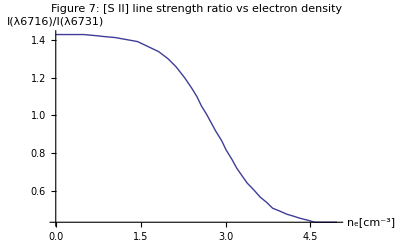

```mathematica
Plotsii
```

### Abundance determinations

Since n_e ~10^2 cm^-3is less than critical density for many elements. So here we use 
		I_i/(I(Hβ))= (α_(eff, i))/(α_eff(Hβ)) n_i/(n(H^+)) 4861/λ_i
		α_(eff, i)= (8.629×10^-6)/T_e^(1/2) ((γ(1,2))_i)/(ω_(1,i))exp(-h⋁_i /kT_e) [cm^3 s^-1]
	If i represent forbiden line, α_(eff,i) are collisional excitation rate and have been calculated in Table 3. If i represent recombination line, α_(eff,i) are recombination rate (Table 4.4-4.6 in AGN2) also listed in Table3. γ(1,2) is collision strengths (Table 3.4-3.10 in AGN2) and ω_1is 1 state weight calculated by (2J+1), ⋁_i  is the frequency of emitted photon from 2 to 1.
	The abundance of elements than can be get as:
		n_i/(n(H^+))=I_i/(I(Hβ))(α_(eff(Hβ)))/(α_(eff, i))λ_i/4861
	For same ions, there are different lines, the total abundance of this ions can be calculated by sum all abudanced calculated by different lines: (n_(i,all))/(n(H^+))=∑(n_(i,lines))/(n(H^+)). The calculated abudance are listed in Table 4. Since there are still some lines we cannot observe, so the abundance is only lower limit.

#### Code (...)

```mathematica
linerefdata31=Lineref[linematchdata3,1];
n[linename_,λb_]:=Table[#[[i,5]]/(λb/.linerefdata3)[[5]] *(λb/.linerefdata3)[[6]]/(#[[i,2]]/.linerefdata3)[[6]]*#[[i,2]]/λb,{i,Length@#}]&@Select[linematchdata3, #[[1]] == linename &]
```

```mathematica
intes=Transpose@{#,Plus@@@Table[n[#[[i]],4861],{i,Length@#}]}&@{"[O III]","[O II]","[O I]","[Ne III]","[Ne V]","[N II]","[S II]","He II","He I"};
cnline=Transpose@{#[[All,1]],Plus@@@Table[intes[[#[[i,2]],2]],{i,Length@#}]}&@{{"O",1;;2},{"Ne",4;;5},{"N",6},{"S",7},{"He",8;;9}};
nlinetable:="Table 4: Abundance of elements \n"Grid[{{Grid[Prepend[intes,{"Elements","n_i/n(H^+)"}],Frame->All],Grid[Prepend[cnline,{"Elements","Abundance"}],Frame->All]}},Alignment->Top]
```

#### Table

```mathematica
nlinetable
```

Table 4: Abundance of elements 
 Elements | n_i/n(H^+)
[O III] | 0.0000587147
[O II] | 0.0000481691
[O I] | 7.84462×10^-6
[Ne III] | 0.0000137346
[Ne V] | 5.35817×10^-6
[N II] | 3.85145×10^-6
[S II] | 1.91323×10^-6
He II | 0.00825185
He I | 0.0998375 | Elements | Abundance
O | 0.000106884
Ne | 0.0000190928
N | 3.85145×10^-6
S | 1.91323×10^-6
He | 0.108089